## Critically Damped Lowpass Phase Plot

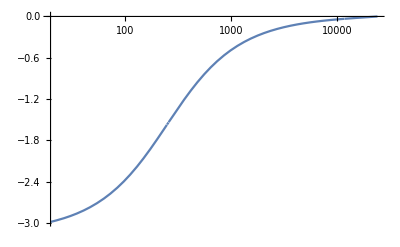

```mathematica
biquadTF[z_,b0_,b1_,b2_,a1_,a2_]:=(b0 z^2 +b1 z + b2)/(-1z^2 -a1 z - a2)
biquadTF1[z_,b0_,b1_,b2_,a1_,a2_]:=(b0+b1 z^(-1) + b2 z^(-2))/(-1 -a1 z^(-1) - a2 z^(-2))

lowpassTF[z_,fc_,sr_]:=Module[{a0,a1, a2,b0, b1, b2,γ,Q=1/2},
γ = Tan[π * fc / sr];

a0= Q*γ^2 + γ + Q;
b0= (Q * γ^2)/a0;
b1= 2 b0;
b2 = b0;
a1 = 2 Q(γ^2-1)/a0;
a2 = (Q γ^2-γ+Q)/a0;

biquadTF1[z,b0,b1,b2,a1,a2]
]

z[ω_,sr_]:=ⅇ^(-2π ⅈ ω / sr)

LogLinearPlot[Arg[lowpassTF[z[ω,48000],250,48000]],{ω,20,24000},PlotRange->All]
```

## First Order Allpass Phase Plot

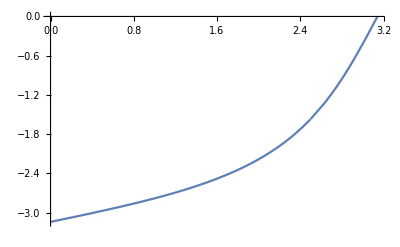

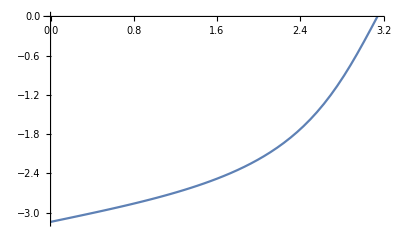

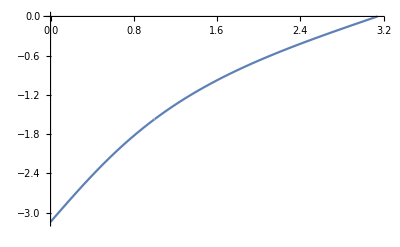

```mathematica
biquadTF1[z_,b0_,b1_,b2_,a1_,a2_]:=(b0+b1 z^(-1) + b2 z^(-2))/(-1 -a1 z ^(-1)- a2 z^(-2))

allpass1TF[z_,β_]:=Module[{a0,a1, a2,b0, b1, b2 (*, γ *)},
(*γ = Tan[π * fc / sr];*)


b0= β;
b1= 1;
b2 = 0;
a1 = β;
a2 = 0;

biquadTF1[z,b0,b1,b2,a1,a2]
]

biquadPR[ω_,b0_,b1_,b2_,a0_,a1_,a2_]:=-ArcTan[(b0 Sin[0 ω]+b1 Sin[1ω]+b2 Sin[2ω]),(b0 Cos[0 ω]+b1 Cos[1ω]+b2 Cos[2ω])]+ArcTan[-(a0 Sin[0 ω]+a1 Sin[1ω]+a2 Sin[2ω]),-(a0 Cos[0 ω]+a1 Cos[1ω]+a2 Cos[2ω])]

allpassPR[ω_,β_]:=Module[{a0,a1, a2,b0, b1, b2 (*, γ *)},
(*γ = Tan[π * fc / sr];*)


b0= β;
b1= 1;
b2 = 0;
a0=1;
a1 = β;
a2 = 0;

(* Mod[biquadPR[z,b0,b1,b2,a0,a1,a2]+π,π]*)
biquadPR[ω,b0,b1,b2,a0,a1,a2]
]

lowpassTF[z_,fc_]:=Module[{a0,a1, a2,b0, b1, b2,γ,Q=1/2},
γ = Tan[ωc/2];

a0= Q*γ^2 + γ + Q;
b0= (Q * γ^2)/a0;
b1= 2 b0;
b2 = b0;
a1 = 2 Q(γ^2-1)/a0;
a2 = (Q γ^2-γ+Q)/a0;

biquadTF1[z,b0,b1,b2,a1,a2]
]

lowpassPR[z_,ωc_]:=Module[{a0,a1, a2,b0, b1, b2,γ,Q=1/2},
γ = Tan[ωc/2];

a0= Q*γ^2 + γ + Q;
b0= (Q * γ^2)/a0;
b1= 2 b0;
b2 = b0;
a1 = 2 Q(γ^2-1)/a0;
a2 = (Q γ^2-γ+Q)/a0;

a0 = 1;

(* Mod[biquadPR[z,b0,b1,b2,a0,a1,a2]+π,π] *)
biquadPR[z,b0,b1,b2,a0,a1,a2]
]

z[ω_,sr_]:=ⅇ^(-2π ⅈ ω / sr)
z[ω_]:=ⅇ^(-ⅈ ω)

β1 = 0.5;
ωc = 1;
Plot[Arg[allpass1TF[z[ω],β1]],{ω,0,π}]
Plot[allpassPR[ω,β1],{ω,0,π}]
Plot[Arg[lowpassTF[z[ω],ωc]],{ω,0,π}]
Plot[lowpassPR[ω,ωc],{ω,0,π}
```

## Try directly solving for β

```mathematica
Clear[ωc,β,ω,lp,ap];

(* simplify the allpass phase response function *)
FullSimplify[allpassPR[ω,β],{Element[β,Reals],Element[ω,Reals]}]
ap[ω_,β_]:=-ArcTan[Sin[ω],β+Cos[ω]]+ArcTan[-β Sin[ω],-1-β Cos[ω]]

(* simplify the lowpass phase response function *)
FullSimplify[lowpassPR[ω,ωc],{Element[ωc,Reals],Element[ω,Reals]}]
lp[ω_,ωc_]:=-ArcTan[Csc[ω/2]^2 Sin[ω]^3 Sin[ωc/2]^2,4 Cos[ω/2]^2 Cos[ω] Sin[ωc/2]^2]+ArcTan[Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])),Cos[ω] (-Cos[ω]+Cos[ωc])-Sin[ω]^2 Sin[ωc]]

(* solve for β in terms of ωc *)
(* Solve[lp[ω,ωc]==ap[ω,β]&&β<1&&β>-1&&ωc>0&&ωc<π&&ω>0&&ω<π,β,Reals] *)

(* simplify the equation *)
eq = FullSimplify[lp[ω,ωc]==ap[ω,β],{Element[ω,Reals],Element[ωc,Reals],Element[β,Reals]}]
```

-ArcTan[Sin[ω],β+Cos[ω]]+ArcTan[-β Sin[ω],-1-β Cos[ω]]

-ArcTan[Csc[ω/2]^2 Sin[ω]^3 Sin[ωc/2]^2,4 Cos[ω/2]^2 Cos[ω] Sin[ωc/2]^2]+ArcTan[Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])),Cos[ω] (-Cos[ω]+Cos[ωc])-Sin[ω]^2 Sin[ωc]]

ArcTan[Sin[ω],β+Cos[ω]]+ArcTan[Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])),Cos[ω] (-Cos[ω]+Cos[ωc])-Sin[ω]^2 Sin[ωc]]==ArcTan[-β Sin[ω],-1-β Cos[ω]]+ArcTan[Csc[ω/2]^2 Sin[ω]^3 Sin[ωc/2]^2,4 Cos[ω/2]^2 Cos[ω] Sin[ωc/2]^2]

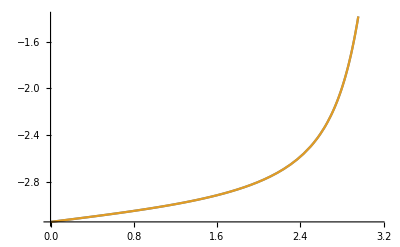

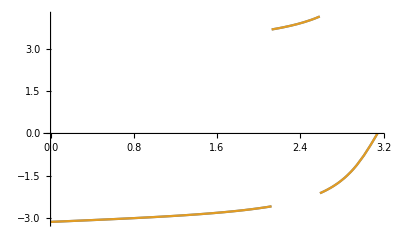

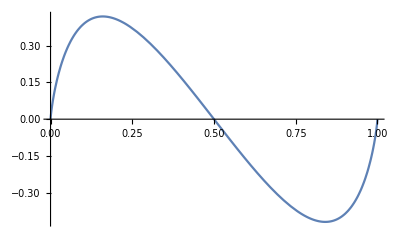

```mathematica
α1 = 0.9;
Plot[{allpassPR[ω,α1*(2) -1],ap[ω,α1*(2) -1]},{ω,0,π}]
Plot[{lowpassPR[ω,α1*(π)],lp[ω,α1*(π)]},{ω,0,π}]

(* ap[π/4,β]//FullSimplify *)
app4[β_]:=-ArcTan[1+√2 β]+ArcTan[-√2 β,-2-√2 β]

(* lp[π/4,ωc]//FullSimplify *)
lpp4[ωc_]:=-ArcTan[Sin[ωc/2]^2,Sin[ωc/2]^2]+ArcTan[-1+√2 Cos[ωc]+Sin[ωc],-1+√2 Cos[ωc]-Sin[ωc]]

Plot[NIntegrate[(ap[ω,α*2-1]-Mod[lp[ω,α*π],π]+π),{ω,0,π}],{α,0,1},PlotRange->All]
(* this is minimised when β = 1/Sqrt[2] *)
```

## Find the frequency ω at which the phase of the allpass filter crosses 90 degrees, for a given filter coefficient β

```mathematica
Solve[allpass1TF[z[ω,2π],β]==z[ω,2π]ⅈ,β]//FullSimplify
(*β[z_]:=-((1-ⅈ)+(1+ⅈ) z^2)/(2 z)*)
β[ω_]:=-Cos[ω]-Sin[ω]
```

{{β→-Cos[ω]-Sin[ω]}}

Test to confirm that this is correct

```mathematica
allpass1TF[z[ω,2π],β[ω]]//FullSimplify
```

ⅈ Cos[ω]+Sin[ω]

```mathematica
allpass1TF[z,β]
```

(1/z+β)/(-1-β/z)

## Find where the phase of the critically-damped lowpass filter crosses 90 degrees

Create a version of the critically damped lowpass transfer function that takes the cutoff frequency in the range from 0 to π with sample rate fixed at 2π:

```mathematica
lowpassTF2[z_,ωc_]:=Module[{a0,a1, a2,b0, b1, b2,γ,Q=1/2},
γ = Tan[ωc/2];

a0= Q*γ^2 + γ + Q;
b0= (Q * γ^2)/a0;
b1= 2 b0;
b2 = b0;
a1 = 2 Q(γ^2-1)/a0;
a2 = (Q γ^2-γ+Q)/a0;

biquadTF1[z,b0,b1,b2,a1,a2]
]
Manipulate[
Plot[Abs[lowpassTF2[z[ω,2π],ωc]],{ω,0,π},PlotRange->{0,1}],
{{ωc,π/2},0,π}]
```

We want to know what cutoff frequency to set so that it goes to 90 degree phase shift at a frequency of ω radians:

```mathematica
FullSimplify[lowpassTF2[z,ωc],Element[ωc,Reals]]
lowpassTF22[z_,ωc_]:=-((1+z)^2 Tan[ωc/2]^2)/(-1+z+(1+z) Tan[ωc/2])^2
lpPhaseOnly[ω_,ωc_]:=lowpassTF22[ω,ωc]/Sqrt[lowpassTF22[ω,ωc]Conjugate[lowpassTF22[ω,ωc]]]
```

-((1+z)^2 Tan[ωc/2]^2)/(-1+z+(1+z) Tan[ωc/2])^2

We plot the phase of this to confirm that it matches the phase plot of the lowpass filter:

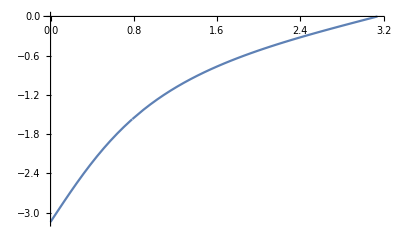

-Graphics-

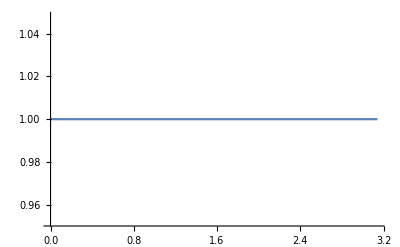

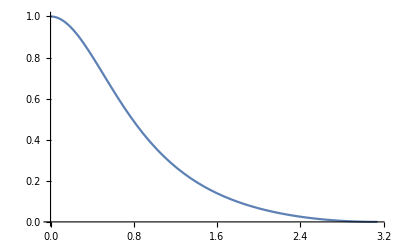

```mathematica
Plot[Arg[lpPhaseOnly[ω,π/4]],{ω,0,π}]
Plot[Arg[lowpassTF22[ω,π/4]],{ω,0,π}]
Plot[Abs[lpPhaseOnly[ω,π/4]],{ω,0,π}]
Plot[Abs[lowpassTF22[ω,π/4]],{ω,0,π}]
```

## The Critically Damped Lowpass Filter can be factored as a pair of first order filters

```mathematica
f=lowpassTF2[z,ωc]//FullSimplify//TrigFactor
f1[z_,ωc_]:=(1+z)/(1+z+(-1+z) Cot[ωc/2])
f1[z,ωc]f1[z,ωc]==-lowpassTF2[z,ωc]//FullSimplify
```

-((1+z)^2 Sin[ωc/2]^2)/((-1+z) Cos[ωc/2]+(1+z) Sin[ωc/2])^2

True

```mathematica
f1[z,ωc]^2//Factor
(1/z+β)/(-1-β/z)
```

(1+z)^2/(1+z-Cot[ωc/2]+z Cot[ωc/2])^2

(1/z+β)/(-1-β/z)

## We try a new formula for phase response, from here: http://www.cmlab.csie.ntu.edu.tw/DSPCourse/slide/Lecture10.pdf

```mathematica
biquadPR[ω_,b0_,b1_,b2_,a0_,a1_,a2_]:=-ArcTan[(b0 Sin[0 ω]+b1 Sin[1ω]+b2 Sin[2ω])/(b0 Cos[0 ω]+b1 Cos[1ω]+b2 Cos[2ω])]+ArcTan[(a0 Sin[0 ω]+a1 Sin[1ω]+a2 Sin[2ω])/(a0 Cos[0 ω]+a1 Cos[1ω]+a2 Cos[2ω])]

allpassPR[z_,β_]:=Module[{a0,a1, a2,b0, b1, b2 (*, γ *)},
(*γ = Tan[π * fc / sr];*)


b0= β;
b1= 1;
b2 = 0;
a0=1;
a1 = β;
a2 = 0;

(* Mod[biquadPR[z,b0,b1,b2,a0,a1,a2]+π,π]*)
biquadPR[z,b0,b1,b2,a0,a1,a2]
]

lowpassPR[z_,ωc_]:=Module[{a0,a1, a2,b0, b1, b2,γ,Q=1/2},
γ = Tan[ωc/2];

a0= Q*γ^2 + γ + Q;
b0= (Q * γ^2)/a0;
b1= 2 b0;
b2 = b0;
a1 = 2 Q(γ^2-1)/a0;
a2 = (Q γ^2-γ+Q)/a0;

a0 = 1;

(* Mod[biquadPR[z,b0,b1,b2,a0,a1,a2]+π,π] *)
biquadPR[z,b0,b1,b2,a0,a1,a2]
]

(* Manipulate[
Plot[allpassPR[ω,β],{ω,0,π},PlotRange->π{-1,1}],
{β,-1,1}
] *)

Manipulate[
Plot[{lowpassPR[ω,ωc],allpassPR[ω,β[ωc]]},{ω,0,π},PlotRange->π{-1,1}],
{{ωc,1},0,π},{{β,0},-1,1}
]
```

```mathematica
lowpassPR[ω,ωc]
allpassPR[ω,β]
lowpassPR[ω,ωc]==allpassPR[ω,β]//FullSimplify
```

-ArcTan[((Sin[ω] Tan[ωc/2]^2)/(1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2)+(Sin[2 ω] Tan[ωc/2]^2)/(2 (1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2)))/(Tan[ωc/2]^2/(2 (1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2))+(Cos[ω] Tan[ωc/2]^2)/(1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2)+(Cos[2 ω] Tan[ωc/2]^2)/(2 (1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2)))]+ArcTan[((Sin[2 ω] (1/2-Tan[ωc/2]+1/2 Tan[ωc/2]^2))/(1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2)+(Sin[ω] (-1+Tan[ωc/2]^2))/(1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2))/(1+(Cos[2 ω] (1/2-Tan[ωc/2]+1/2 Tan[ωc/2]^2))/(1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2)+(Cos[ω] (-1+Tan[ωc/2]^2))/(1/2+Tan[ωc/2]+1/2 Tan[ωc/2]^2))]

-ArcTan[Sin[ω]/(β+Cos[ω])]+ArcTan[(β Sin[ω])/(1+β Cos[ω])]

```mathematica
ArcCot[(β+Cos[ω]) Csc[ω]]==ArcTan[(β Sin[ω])/(1+β Cos[ω])]+ArcTan[(Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])))/(Cos[ω]^2-Cos[ω] Cos[ωc]+Sin[ω]^2 Sin[ωc])]+ArcTan[Tan[ω]]
```

ArcCot[(β+Cos[ω]) Csc[ω]]==ArcTan[(β Sin[ω])/(1+β Cos[ω])]+ArcTan[(Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])))/(Cos[ω]^2-Cos[ω] Cos[ωc]+Sin[ω]^2 Sin[ωc])]+ArcTan[Tan[ω]]

```mathematica
FullSimplify[lowpassPR[ω,ωc]==π/2]
soln = Solve[π+2 ArcTan[(Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])))/(Cos[ω]^2-Cos[ω] Cos[ωc]+Sin[ω]^2 Sin[ωc])]+2 ArcTan[Tan[ω]]==0,ωc];
FullSimplify[soln]
```

π+2 ArcTan[(Sin[ω] (Cos[ωc]+Cos[ω] (-1+Sin[ωc])))/(Cos[ω]^2-Cos[ω] Cos[ωc]+Sin[ω]^2 Sin[ωc])]+2 ArcTan[Tan[ω]]==0

{{ωc→ConditionalExpression[ArcTan[Sec[ω-ArcTan[Tan[ω]]]/(√(Sec[ω]^2)),1/(√(Csc[ω]^2))]+2 π C[1],C[1]∈ℤ&&(-π<Re[ArcTan[Tan[ω]]]<0||(Im[ArcTan[Tan[ω]]]>0&&-π<Re[ArcTan[Tan[ω]]]≤0)||(-π≤Re[ArcTan[Tan[ω]]]<0&&Im[ArcTan[Tan[ω]]]<0))]},{ωc→ConditionalExpression[ArcTan[Sec[ω-ArcTan[Tan[ω]]]/(√(Sec[ω]^2)),-1/(√(Csc[ω]^2))]+2 π C[1],C[1]∈ℤ&&(-π<Re[ArcTan[Tan[ω]]]<0||(Im[ArcTan[Tan[ω]]]>0&&-π<Re[ArcTan[Tan[ω]]]≤0)||(-π≤Re[ArcTan[Tan[ω]]]<0&&Im[ArcTan[Tan[ω]]]<0))]}}

## This looks like the solution!!!

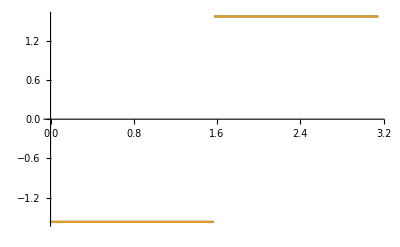

```mathematica
ωclp[ω_]:=ArcTan[Sec[ω-ArcTan[Tan[ω]]]/(√(Sec[ω]^2)),1/(√(Csc[ω]^2))]
ωclp2[ω_]:=ArcTan[Sec[π]/(√(Sec[ω]^2)),1/(√(Csc[ω]^2))]
ωclp3[ω_]:=ArcTan[1/(√(Sec[ω]^2)),1/(√(Csc[ω]^2))]
Plot[{lowpassPR[ω,ω],lowpassPR[ω,ωclp[ω]]},{ω,0,π}]
```

```mathematica
Manipulate[
Plot[{lowpassPR[ω,ωclp[ωc]],allpassPR[ω,β[ωc]]},{ω,0,π},PlotRange->π{-1,1}],
{{ωc,1},0,π}
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

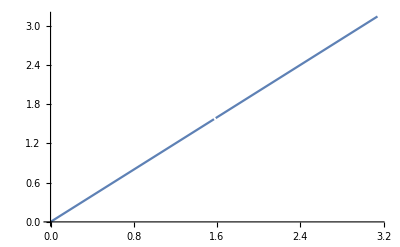

```mathematica
Plot[ωclp[ω],{ω,0,π}]
```

```mathematica
allpassPR[ω,beta]//FullSimplify
```

-ArcCot[(beta+Cos[ω]) Csc[ω]]+ArcTan[(beta Sin[ω])/(1+beta Cos[ω])]

```mathematica
Plot[NIntegrate[(ap[ω,2α - 1]-Mod[lp[ω,α*π],π]+π),{ω,0,π}],{α,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Table[
NMinimize[
NIntegrate[(ap[ω,β]-Mod[lp[ω,ωc],π]+π),{ω,0,π}]^2,
β],
{ωc,0.01,π-0.01,0.05}
]
```

NIntegrate::inumr: The integrand π-ArcTan[Sin[ω],β+Cos[ω]]+ArcTan[-β Sin[ω],-1-β Cos[ω]]-Mod[ArcTan[(0.99995+Times[«2»]) Sin[ω],Plus[«2»] Cos[«1»]-0.00999983 Power[«2»]]-ArcTan[0.0000249998 Power[«2»] Power[«2»],0.0000999992 Power[«2»] Cos[«1»]],π] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.19048}. NIntegrate obtained 0.0000107015 and 0.00207639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.28251}. NIntegrate obtained 0.0000146585 and 0.00250448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.3316}. NIntegrate obtained -0.0000253904 and 0.00152934 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.80297×10^-31,{β→-0.99005}},{9.87894×10^-33,{β→-0.941731}},{8.01731×10^-32,{β→-0.895635}},{1.79586×10^-30,{β→-0.851559}},{5.33491×10^-32,{β→-0.80932}},{1.86505×10^-31,{β→-0.768757}},{4.54045×10^-34,{β→-0.729725}},{2.49743×10^-31,{β→-0.692091}},{5.90037×10^-33,{β→-0.655738}},{1.26637×10^-31,{β→-0.620557}},{6.47336×10^-32,{β→-0.586452}},{3.76209×10^-33,{β→-0.553333}},{2.6801×10^-30,{β→-0.521117}},{1.41586×10^-32,{β→-0.48973}},{1.71579×10^-29,{β→-0.459103}},{5.09651×10^-33,{β→-0.429171}},{6.16477×10^-31,{β→-0.399874}},{9.84939×10^-34,{β→-0.371158}},{2.62711×10^-32,{β→-0.34297}},{5.96045×10^-36,{β→-0.315261}},{6.25209×10^-33,{β→-0.287985}},{7.1617×10^-34,{β→-0.2611}},{3.22264×10^-33,{β→-0.234563}},{9.6205×10^-31,{β→-0.208336}},{1.36503×10^-32,{β→-0.182381}},{8.46791×10^-30,{β→-0.156661}},{8.38068×10^-34,{β→-0.131142}},{3.32654×10^-32,{β→-0.10579}},{1.35499×10^-33,{β→-0.0805718}},{2.06457×10^-31,{β→-0.0554549}},{2.59781×10^-32,{β→-0.0304075}},{6.88513×10^-31,{β→-0.00539822}},{7.66973×10^-33,{β→0.0196043}},{4.47032×10^-33,{β→0.0446314}},{8.22717×10^-33,{β→0.0697144}},{1.7988×10^-28,{β→0.0948851}},{1.43394×10^-32,{β→0.120175}},{3.43326×10^-32,{β→0.145618}},{7.19021×10^-29,{β→0.171247}},{4.50849×10^-34,{β→0.197096}},{2.70989×10^-32,{β→0.223201}},{7.7858×10^-32,{β→0.2496}},{2.51369×10^-34,{β→0.27633}},{2.19763×10^-32,{β→0.303431}},{7.40895×10^-32,{β→0.330948}},{2.35926×10^-31,{β→1.73383}},{4.5774×10^-32,{β→0.387405}},{5.10805×10^-31,{β→1.53908}},{2.4787×10^-31,{β→1.45859}},{7.70372×10^-32,{β→1.39019}},{8.13845×10^-6,{β→1.33227}},{1.09783×10^-30,{β→1.27762}},{3.80593×10^-31,{β→0.572033}},{2.08148×10^-29,{β→1.18933}},{7.51233×10^-32,{β→1.15272}},{2.22676×10^-8,{β→1.12034}},{7.69358×10^-33,{β→0.713308}},{2.64467×10^-32,{β→0.751721}},{1.52458×10^-30,{β→0.791606}},{8.99333×10^-32,{β→0.833102}},{1.10006×10^-28,{β→0.876364}},{3.28166×10^-31,{β→0.921564}},{1.09431×10^-28,{β→0.968896}}}

```mathematica
result =β/.#[[2]]&/@ {{1.802970771973875*^-31,{β->-0.9900496687367508}},{9.878941537318814*^-33,{β->-0.9417306001272803}},{8.017309286626477*^-32,{β->-0.8956348283318336}},{1.7958645553946772*^-30,{β->-0.8515585089091241}},{5.334911650599289*^-32,{β->-0.809320122950462}},{1.8650476412154149*^-31,{β->-0.768757401170438}},{4.540445620223429*^-34,{β->-0.729724736722191}},{2.49742860321326*^-31,{β->-0.6920909980006602}},{5.9003672317136*^-33,{β->-0.6557376706033378}},{1.2663704555343273*^-31,{β->-0.6205572715549967}},{6.473357533068332*^-32,{β->-0.5864519898243146}},{3.7620868952669086*^-33,{β->-0.5533325157736263}},{2.68010491501806*^-30,{β->-0.5211170290172559}},{1.4158628280262748*^-32,{β->-0.48973031961752467}},{1.715788458259852*^-29,{β->-0.4591030219230347}},{5.0965080610572416*^-33,{β->-0.42917094388215304}},{6.164769081997471*^-31,{β->-0.39987447752350846}},{9.84938991480572*^-34,{β->-0.37115807862192524}},{2.6271067082399347*^-32,{β->-0.3429698054697271}},{5.960446702175606*^-36,{β->-0.3152609082330376}},{6.252092671902255*^-33,{β->-0.28798546165656}},{7.161703580172825*^-34,{β->-0.2611000349400807}},{3.222642966331438*^-33,{β->-0.23456339348686758}},{9.620501987261615*^-31,{β->-0.20833622795100698}},{1.3650294813120644*^-32,{β->-0.18238090661372003}},{8.46791008018427*^-30,{β->-0.15666124761885689}},{8.380681969744342*^-34,{β->-0.1311423080118541}},{3.3265353677184216*^-32,{β->-0.10579018686809337}},{1.3549915589651208*^-33,{β->-0.08057184007647289}},{2.0645714818952723*^-31,{β->-0.05545490457097036}},{2.5978088688185607*^-32,{β->-0.03040752998365622}},{6.885132437353309*^-31,{β->-0.0053982158325225705}},{7.669725423067696*^-33,{β->0.019604347539414018}},{4.470320878478172*^-33,{β->0.044631435987993455}},{8.227171499241732*^-33,{β->0.06971444823163386}},{1.7988007371082923*^-28,{β->0.0948850638251436}},{1.4339403795698967*^-32,{β->0.12017540413788183}},{3.433260134188995*^-32,{β->0.1456181980859454}},{7.19020989333768*^-29,{β->0.17124695445606627}},{4.508490927913339*^-34,{β->0.1970961427826953}},{2.709891272479643*^-32,{β->0.2232013849021239}},{7.78580192964243*^-32,{β->0.24959965951369742}},{2.5136926844250414*^-34,{β->0.2763295223343681}},{2.1976309208463185*^-32,{β->0.30343134474652045}},{7.408950213341535*^-32,{β->0.3309475742203549}},{2.359264181874364*^-31,{β->1.7338323998529501}},{4.577396499500625*^-32,{β->0.38740517012480385}},{5.108047695001046*^-31,{β->1.5390779207060705}},{2.4787019310817536*^-31,{β->1.458591149784049}},{7.703719777548943*^-32,{β->1.390189985170451}},{8.138445372958364*^-6,{β->1.3322700834432775}},{1.0978282165493341*^-30,{β->1.2776189413854828}},{3.805927222755729*^-31,{β->0.5720332585946518}},{2.0814788800518862*^-29,{β->1.1893283647498947}},{7.512330489325462*^-32,{β->1.15271956699655}},{2.2267612693699817*^-8,{β->1.1203392539644843}},{7.693579128450453*^-33,{β->0.7133080836699481}},{2.644671160305843*^-32,{β->0.7517213089166049}},{1.524576073200108*^-30,{β->0.7916063017691743}},{8.993333728296565*^-32,{β->0.8331021703027449}},{1.1000592295283156*^-28,{β->0.8763636959223261}},{3.281657196418667*^-31,{β->0.9215637380784185}},{1.0943081075245331*^-28,{β->0.9688960868863293}}}
```

{-0.99005,-0.941731,-0.895635,-0.851559,-0.80932,-0.768757,-0.729725,-0.692091,-0.655738,-0.620557,-0.586452,-0.553333,-0.521117,-0.48973,-0.459103,-0.429171,-0.399874,-0.371158,-0.34297,-0.315261,-0.287985,-0.2611,-0.234563,-0.208336,-0.182381,-0.156661,-0.131142,-0.10579,-0.0805718,-0.0554549,-0.0304075,-0.00539822,0.0196043,0.0446314,0.0697144,0.0948851,0.120175,0.145618,0.171247,0.197096,0.223201,0.2496,0.27633,0.303431,0.330948,1.73383,0.387405,1.53908,1.45859,1.39019,1.33227,1.27762,0.572033,1.18933,1.15272,1.12034,0.713308,0.751721,0.791606,0.833102,0.876364,0.921564,0.968896}

-2.+1.27324 ωc+0.731239 Cos[0.5 ωc]+0.268761 Cos[ωc]-0.731239 Sin[0.5 ωc]

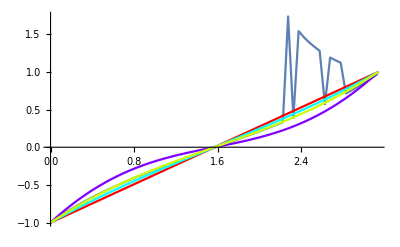

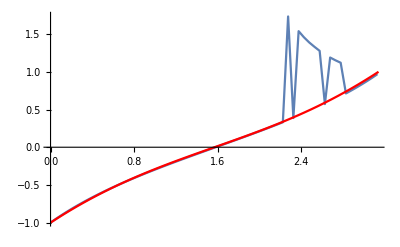

```mathematica
β[x_]:=α(2(2x/π-1)-(Sin[x/2]-Cos[x/2]))+(1-α)(2(2x/π-1)+(Cos[x]))
FullSimplify[β[ωc]//N]
βn[ωc_]:=-2.+1.2732395447351628 ωc+0.7312388979353096 Cos[0.5 ωc]+0.26876110206469045 Cos[ωc]-0.7312388979353096 Sin[0.5 ωc]

α = -1+√2+√(10-7 √2);

Show[ListLinePlot[result,DataRange->{0.01,π-0.01}],Plot[2x/π-1,{x,0,π},PlotStyle->Hue[0]],Plot[2(2x/π-1)-(Sin[x/2]-Cos[x/2]),{x,0,π},PlotStyle->Hue[0.5]],
Plot[2(2x/π-1)+(Cos[x]),{x,0,π},PlotStyle->Hue[0.75]],
Plot[α(2(2x/π-1)-(Sin[x/2]-Cos[x/2]))+(1-α)(2(2x/π-1)+(Cos[x])),{x,0,π},PlotStyle->Hue[0.2]]
]

Show[ListLinePlot[result,DataRange->{0.01,π-0.01}],Plot[βn[ωc],{ωc,0,π},PlotStyle->Hue[0]]
]
```

```mathematica
NMinimize[
NIntegrate[(ap[ω,β]-Mod[lp[ω,π/4],π]+π),{ω,0,π}]^2,
β]
```

NIntegrate::inumr: The integrand π-ArcTan[Sin[ω],β+Cos[ω]]+ArcTan[-β Sin[ω],-1-β Cos[ω]]-Mod[ArcTan[(Power[«2»]+Times[«2»]) Sin[ω],Plus[«2»] Cos[«1»]-Power[«2»] Power[«2»]]-ArcTan[Power[«2»] Power[«2»] Power[«2»],4 Power[«2»] Cos[«1»] Power[«2»]],π] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1.20009×10^-31,{β→-0.414214}}

```mathematica
x = π/4
1-Sqrt[2]//N
Clear[α];
Solve[α(2(2x/π-1)-(Sin[x/2]-Cos[x/2]))+(1-α)(2(2x/π-1)+(Cos[x]))==1-Sqrt[2],α]//FullSimplify
a=(2(2x/π-1)-(Sin[x/2]-Cos[x/2]))
b=(2(2x/π-1)+(Cos[x]))
α a + (1-α)b==1-Sqrt[2]
α (a - b)==(1-Sqrt[2]-b)/(a-b)
α=(1-Sqrt[2]-b)/(a-b)//FullSimplify
```

π/4

-0.414214

{{α→-1+√2+√(10-7 √2)}}

-1+Cos[π/8]-Sin[π/8]

-1+1/(√2)

(-1+1/(√2)) (1-α)+α (-1+Cos[π/8]-Sin[π/8])==1-√2

α (-1/(√2)+Cos[π/8]-Sin[π/8])==(2-1/(√2)-√2)/(-1/(√2)+Cos[π/8]-Sin[π/8])

-1+√2+√(10-7 √2)

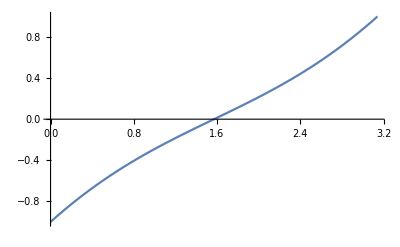

-2. + 1.2732395447351628*ωc + 0.7312388979353096*Cos(0.5*ωc) + 
   0.26876110206469045*Cos(ωc) - 0.7312388979353096*Sin(0.5*ωc)

```mathematica
βn[ωc_]:=-2.+1.2732395447351628 ωc+0.7312388979353096 Cos[0.5 ωc]+0.26876110206469045 Cos[ωc]-0.7312388979353096 Sin[0.5 ωc]
Plot[{βn[ωc]},{ωc,0,π}]
βn[ωc]//CForm
```

```mathematica
c1 = -1+Sqrt[2]+Sqrt[10-7 Sqrt[2]]
c2 = 4/π
c3 = 1-c1
βn[ωc_]:=-2 + c2 ωc + c1 (Cos[ωc/2]-Sin[ωc/2])+c3 Cos[ωc]
βn[ωc]
```

-1+√2+√(10-7 √2)

4/π

2-√2-√(10-7 √2)

-2+(4 ωc)/π+(2-√2-√(10-7 √2)) Cos[ωc]+(-1+√2+√(10-7 √2)) (Cos[ωc/2]-Sin[ωc/2])

```mathematica
c1//CForm
```

-1 + Sqrt(2) + Sqrt(10 - 7*Sqrt(2))